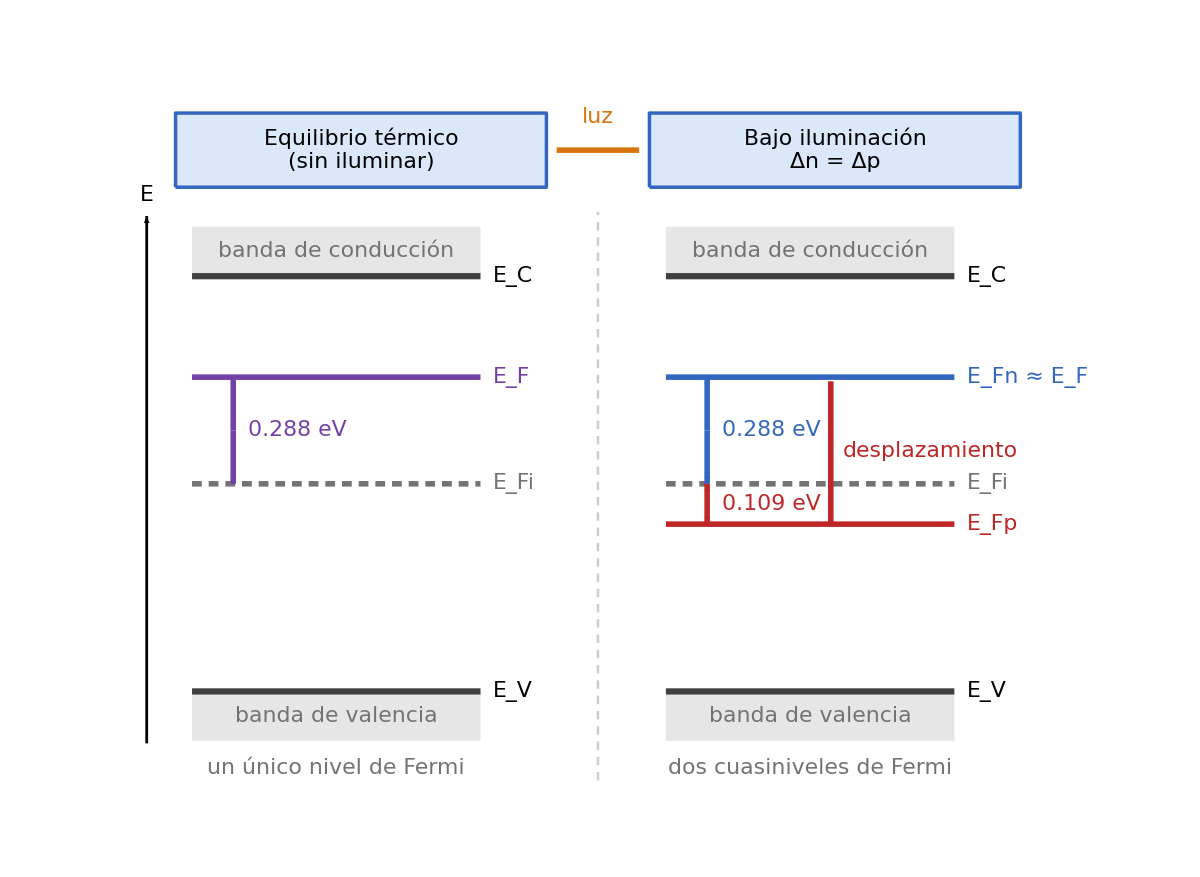

```mathematica
diagramaCuasiniveles = Module[
  {fs, cAzul, cAzulB, cRojo, cVio, cNar, cGris, mostrarValores,
   kT, ni, Nd, dn, p0, EF, EFn, EFp, eg, se, Lw, pxL, pxR,
   ey, ins, insI, flecha, caja, fmt, nivel, cota, banda},

  (* ---------- Parámetros globales ---------- *)
  fs = 22;                  (* tamaño de fuente único para todo el gráfico *)
  mostrarValores = True;    (* False oculta las cotas numéricas *)
  cAzul = RGBColor[0.86, 0.91, 0.98];  cAzulB = RGBColor[0.20, 0.40, 0.75];
  cRojo = RGBColor[0.75, 0.15, 0.15];  cVio   = RGBColor[0.45, 0.25, 0.65];
  cNar  = RGBColor[0.85, 0.45, 0.05];  cGris  = GrayLevel[0.45];

  (* ---------- Datos del ejemplo (eV, cm^-3) ---------- *)
  kT = 0.0259;  ni = 1.5*10^10;  Nd = 10^15;  dn = 10^12;
  p0  = ni^2/Nd;
  EF  = kT Log[Nd/ni];             (* E_F  - E_Fi, equilibrio *)
  EFn = kT Log[(Nd + dn)/ni];      (* E_Fn - E_Fi *)
  EFp = -kT Log[(p0 + dn)/ni];     (* E_Fp - E_Fi (por debajo de E_Fi) *)

  (* ---------- Geometría ---------- *)
  eg = 1.12;                       (* banda prohibida del Si (eV): solo fija la escala del dibujo *)
  se = 9;                          (* unidades de dibujo por eV *)
  Lw = 7;                          (* longitud de los niveles *)
  {pxL, pxR} = {2.0, 13.5};        (* origen horizontal de cada panel *)
  ey[en_] := se en;

  (* ---------- Funciones auxiliares ---------- *)
  ins[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos];
  insI[expr_, pos_, col_: Black] := Inset[Style[expr, fs, col], pos, {Left, Center}];
  flecha[p1_, p2_, col_, s_: 0.025] :=
    {col, AbsoluteThickness[4], Arrowheads[s], Arrow[{p1, p2}]};
  caja[{xc_, yc_}, {w_, h_}, relleno_, borde_] :=
    {EdgeForm[{AbsoluteThickness[2.5], borde}], relleno,
     Rectangle[{xc - w/2, yc - h/2}, {xc + w/2, yc + h/2}, RoundingRadius -> 0.15]};
  fmt[x_] := ToString[NumberForm[x, {3, 3}]];

  nivel[px_, en_, col_, dash_] :=
    {col, AbsoluteThickness[4], AbsoluteDashing[dash],
     Line[{{px, ey[en]}, {px + Lw, ey[en]}}]};

  cota[x_, e1_, e2_, col_] := Module[{ym = (ey[e1] + ey[e2])/2},
    {flecha[{x, ym}, {x, ey[e1]}, col, 0.014],
     flecha[{x, ym}, {x, ey[e2]}, col, 0.014],
     insI[Row[{fmt[Abs[e1 - e2]], " eV"}], {x + 0.35, ym}, col]}];

  banda[px_] := {
    {GrayLevel[0.90], EdgeForm[None],
     Rectangle[{px, ey[eg/2]}, {px + Lw, ey[eg/2] + 1.2}],
     Rectangle[{px, -ey[eg/2] - 1.2}, {px + Lw, -ey[eg/2]}]},
    {GrayLevel[0.25], AbsoluteThickness[4.5],
     Line[{{px, ey[eg/2]}, {px + Lw, ey[eg/2]}}],
     Line[{{px, -ey[eg/2]}, {px + Lw, -ey[eg/2]}}]},
    ins["banda de conducción", {px + Lw/2, ey[eg/2] + 0.6}, cGris],
    ins["banda de valencia", {px + Lw/2, -ey[eg/2] - 0.6}, cGris],
    insI[Row[{Subscript["E", "C"]}], {px + Lw + 0.3, ey[eg/2]}],
    insI[Row[{Subscript["E", "V"]}], {px + Lw + 0.3, -ey[eg/2]}]};

  (* ---------- Diagrama ---------- *)
  Graphics[{
    (* separador entre los dos casos *)
    {GrayLevel[0.8], AbsoluteThickness[1.8], AbsoluteDashing[{6, 5}],
     Line[{{11.85, -7.2}, {11.85, 6.6}}]},

    (* eje de energía *)
    {Black, AbsoluteThickness[2], Arrowheads[0.02],
     Arrow[{{0.9, -6.3}, {0.9, 6.5}}]},
    ins[Style["E", Italic], {0.9, 7.0}],

    (* cabeceras y paso de un caso al otro *)
    caja[{6.1, 8.1}, {9.0, 1.8}, cAzul, cAzulB],
    ins[Column[{"Equilibrio térmico", "(sin iluminar)"}, Center], {6.1, 8.1}],
    caja[{17.6, 8.1}, {9.0, 1.8}, cAzul, cAzulB],
    ins[Column[{"Bajo iluminación",
       Row[{"Δ", Style["n", Italic], " = ",
         "Δ", Style["p", Italic]}]}, Center], {17.6, 8.1}],
    flecha[{10.85, 8.1}, {12.85, 8.1}, cNar],
    ins["luz", {11.85, 8.9}, cNar],

    (* panel izquierdo: equilibrio *)
    banda[pxL],
    nivel[pxL, 0, cGris, {7, 5}],
    nivel[pxL, EF, cVio, {}],
    insI[Row[{Subscript["E", "Fi"]}], {pxL + Lw + 0.3, 0}, cGris],
    insI[Row[{Subscript["E", "F"]}], {pxL + Lw + 0.3, ey[EF]}, cVio],
    If[mostrarValores, cota[pxL + 1.0, 0, EF, cVio], {}],
    ins["un único nivel de Fermi", {pxL + Lw/2, -6.9}, cGris],

    (* panel derecho: cuasiniveles de Fermi *)
    banda[pxR],
    nivel[pxR, 0, cGris, {7, 5}],
    nivel[pxR, EFn, cAzulB, {}],
    nivel[pxR, EFp, cRojo, {}],
    insI[Row[{Subscript["E", "Fi"]}], {pxR + Lw + 0.3, 0}, cGris],
    insI[Row[{Subscript["E", "Fn"], " ≈ ", Subscript["E", "F"]}],
     {pxR + Lw + 0.3, ey[EFn]}, cAzulB],
    insI[Row[{Subscript["E", "Fp"]}], {pxR + Lw + 0.3, ey[EFp]}, cRojo],
    If[mostrarValores,
     {cota[pxR + 1.0, 0, EFn, cAzulB], cota[pxR + 1.0, EFp, 0, cRojo]}, {}],
    flecha[{pxR + 4.0, ey[EFn] - 0.1}, {pxR + 4.0, ey[EFp]}, cRojo],
    insI["desplazamiento", {pxR + 4.3, (ey[EFn] + ey[EFp])/2}, cRojo],
    ins["dos cuasiniveles de Fermi", {pxR + Lw/2, -6.9}, cGris]
   },
   ImageSize -> 1200,
   PlotRange -> {{0, 23.8}, {-7.6, 9.8}},
   PlotRangePadding -> None,
   AspectRatio -> 17.4/23.8,
   Background -> White]
];
diagramaCuasiniveles
```